Last modified on: Tuesday, July 10, 2018 at 23:12

Author Info

Andreia Ribeiro de Noronha Sales

Amir Azadi

University of Colorado at Boulder

Poster Session Content

Spectral Identification Classifier

The goal of the project was to train a classifier to determine the chemical composition of a light source when given its spectrum. This applies to spectra of stars, galaxies, planets, atmospheres and more, and it can be useful for remote sensing, astrophysics and planetary sciences.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

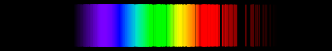
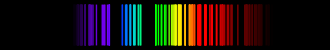
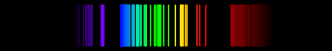
spectrumIdentify[-Graphics-]
"Hydrogen I-Helium I-Sodium I-Neon I"
spectrumIdentify[-Graphics-]
"Hydrogen I-Helium I-Carbon I-Oxygen I-Silicon I"
spectrumIdentify[-Graphics-,3]
{{"Mercury I"}→1.,{"Carbon I-Oxygen I-Nitrogen I-Hydrogen I-Argon I-Neon I-Helium I-Krypton I"}→2.88246×10^-7,{"Tungsten I"}→9.92641×10^-8}

The classifier function identifies 97 neutral elements, 8 most common ions, and 47 most common compounds and combinations, including the typical ones that are found in stars, planetary atmospheres, galaxies, and nebulae. The classifier function exhibits 86.2% accuracy when trained on numerical data using the NearestNeighbors method. The accuracy improves to 97.2% when the classifier is trained on images using the LogisticRegression method.

In the future, the classifier function can be expanded to support more ions and combinations, and accuracy can be improved by training Classify on more data samples. The classifier is trained on highly accurate and detailed data, so it does not work very well with lower definition spectra. This can be improved by adding lower definition data to the classifier. It can also be expanded to account for Doppler shifting, which is very useful for investigating the motion of the light source.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Spectral Analysis

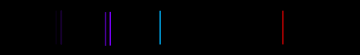

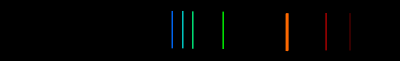

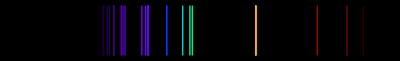

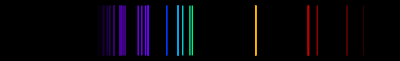

Method

Numerical Sequence Input
-Graphics--Graphics-

Image Input
-Graphics--Graphics-

Conclusion

Machine learning as the future of spectroscopy

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

The first step is to generate enough spectra using the wavelength data available through the built-in function SpectralLineData. Random noise is generated and added to each line value. The added noise is two orders of magnitude bigger than the precision in the original data, which should be enough to account for quantum broadening of the lines and other general measurement uncertainty. Thread is used to associate the wavelengths to the corresponding element. The process should be repeated at least 100 times for each element and ion. Once that data is produced and saved, the tables of spectra with random noise can be combined to form compounds. 

The complete data set is created by joining all element, ion, and compound tables. 
The data set is then used to train Classify. The total number of classes for the wavelength data is 151. The function takes 1min 28s to train and the accuracy is 86.2% when using the NearestNeighbors method. The following methods are also tested: DecisionTree, GradientBoostedTrees, LogisticRegression, Markov, NaiveBayes, NeuralNetwork, RandomForest, and SupportVectorMachine. Most of them exhibit slightly lower accuracy than NearestNeighbors, but still show above 84% success. NeuralNetwork and SupportVectorMachine both perform poorly, exhibiting less than 4% accuracy. 

Once the wavelength classifier function is trained, the next step is to train a classifier on the images of the spectra. Data is again generated using SpectralLineData and random noise is added to the lines. Thread is used for the element associations. 
Again, compounds can be generated by combining tables of pure elements. The complete data set is created by joining all element, ion, and compound tables. 
The data is saved and used to train the classifier function on the images. The total number of classes is 140. The function takes 9min 41s to train and the accuracy is 97.2% when using the LogisticRegression method. No other methods are tested due to time constraints.

Finally, an identification function is created to accept both numerical sequences and images as the input and runs it through the appropriate classifier function. The output is the chemical composition of the input.

#### Code

```mathematica
(* linedata generates spectral lines for element "elem" and ionization level "ion" *)
linedata[elem_,ion_]:=Part[{lines=SpectralLineData[EntityClass["AtomicLine",{elem,ion}],{Quantity[300.000, "Nanometers"],Quantity[800.000, "Nanometers"]}];,wavelength=QuantityMagnitude[SpectralLineData[lines,"Wavelength"],"Nanometers"]},2];

(* iongenerate generates "n" (numerical) spectra with random noise of element "elem" and ionization level "ion" and matches them with the corresponding element *)
iongenerate[elem_,ion_,n_]:=Thread[Table[linedata[elem,ion]+RandomReal[0.1],n]-> elem <>" "<>RomanNumeral[ion]];

(* here, elem1 and elem2 are tables of two different elements made using iongenerate, mixgenerate takes the two tables and creates a compound *)
mixgenerate[elem1_,elem2_]:=Part[{wdata=Table[Flatten[Join[{elem1[[i,1]],elem2[[i,1]]}]],{i,1,100}];,
ldata=Flatten[Table[{elem1[[1,2]]<>"-"<>elem2[[1,2]]}, {i,1,100}]];,compounds=Thread[wdata-> ldata]},3];

(* spectrumgenerate generates "n" (visual) spectra with random noise of element "elem" and ionization level "ion" and matches them with the corresponding element *)
spectrumgenerate[elem_,ion_,n_]:=Thread[Table[Part[{lines=SpectralLineData[EntityClass["AtomicLine",{elem,ion}],{Quantity[300.000, "Nanometers"],Quantity[800.000, "Nanometers"]}];,wavelength=QuantityMagnitude[SpectralLineData[lines,"Wavelength"],"Nanometers"]+RandomReal[0.1];,Graphics[{ColorData["VisibleSpectrum"][#],Line[{{#,0},{#,1}}]}&/@wavelength,AspectRatio->1/6.5,Background->Black]},3],n]-> elem<>" "<>RomanNumeral[ion]];

(* here, elem1, elem2, etc. are tables of different elements generated using spectrumgenerate, spmix takes these tables and creates compounds of up to 8 elements. This can be increased by adding more arguments to the function *)
spmix[elem1_,elem2_]:=Thread[Show[elem1[[1,1]],elem2[[1,1]]]-> elem1[[1,2]]<>", "<>elem2[[1,2]]];
spmix[elem1_,elem2_,elem3_]:=Thread[Show[elem1[[1,1]],elem2[[1,1]],elem3[[1,1]]]-> elem1[[1,2]]<>", "<>elem2[[1,2]]<>", "<>elem3[[1,2]]];
spmix[elem1_,elem2_,elem3_,elem4_]:=Thread[Show[elem1[[1,1]],elem2[[1,1]],elem3[[1,1]],elem4[[1,1]]]-> elem1[[1,2]]<>", "<>elem2[[1,2]]<>", "<>elem3[[1,2]]<>", "<>elem4[[1,2]]];
spmix[elem1_,elem2_,elem3_,elem4_,elem5_]:=Thread[Show[elem1[[1,1]],elem2[[1,1]],elem3[[1,1]],elem4[[1,1]],elem5[[1,1]]]-> elem1[[1,2]]<>", "<>elem2[[1,2]]<>", "<>elem3[[1,2]]<>", "<>elem4[[1,2]]<>", "<>elem5[[1,2]]];
spmix[elem1_,elem2_,elem3_,elem4_,elem5_,elem6_]:=Thread[Show[elem1[[1,1]],elem2[[1,1]],elem3[[1,1]],elem4[[1,1]],elem5[[1,1]],elem6[[1,1]]]-> elem1[[1,2]]<>", "<>elem2[[1,2]]<>", "<>elem3[[1,2]]<>", "<>elem4[[1,2]]<>", "<>elem5[[1,2]]<>", "<>elem6[[1,2]]];
spmix[elem1_,elem2_,elem3_,elem4_,elem5_,elem6_,elem7_]:=Thread[Show[elem1[[1,1]],elem2[[1,1]],elem3[[1,1]],elem4[[1,1]],elem5[[1,1]],elem6[[1,1]],elem7[[1,1]]]-> elem1[[1,2]]<>", "<>elem2[[1,2]]<>", "<>elem3[[1,2]]<>", "<>elem4[[1,2]]<>", "<>elem5[[1,2]]<>", "<>elem6[[1,2]]<>", "<>elem7[[1,2]]];
spmix[elem1_,elem2_,elem3_,elem4_,elem5_,elem6_,elem7_,elem8_]:=Thread[Show[elem1[[1,1]],elem2[[1,1]],elem3[[1,1]],elem4[[1,1]],elem5[[1,1]],elem6[[1,1]],elem7[[1,1]],elem8[[1,1]]]-> elem1[[1,2]]<>", "<>elem2[[1,2]]<>", "<>elem3[[1,2]]<>", "<>elem4[[1,2]]<>", "<>elem5[[1,2]]<>", "<>elem6[[1,2]]<>", "<>elem7[[1,2]]<>", "<>elem8[[1,2]]];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/andreiasales/Desktop/Wolram Summer 2018/Summer2018Starter-master

```mathematica
(* import mixdata and spdata from the location where they are saved. mixdata has wavelength data matched with the corresponding compositions of 151 classes. spdata has images of spectra with corresponding compositions of 140 classes. *)
```

```mathematica
mixdata=Import["/Users/andreiasales/Desktop/Wolram Summer 2018/Summer2018Starter-master/mixdata.mx"];
```

```mathematica
spdata=Import["/Users/andreiasales/Desktop/Wolram Summer 2018/Summer2018Starter-master/spdata.mx"];
```

```mathematica
(* import the classifier functions. elementClassify was trained using numerical values for the wavelengths. spectrumClassify was trained using images of the spectra. Import them with same name for spectrumIdentify to work or change spectrumIdentify function accordingly *)
elementClassify=Import["/Users/andreiasales/Desktop/Wolram Summer 2018/Summer2018Starter-master/elementClassify10.wmlf"];
```

```mathematica
spectrumClassify=Import["/Users/andreiasales/spectrumClassify.wmlf"];
```

```mathematica
(* spectrumIdentify tests if the input is a list. If yes, it uses elementClassify to identify the composition. If not, it uses spectrumClassify. Give "max" to get top probabilities *)
spectrumIdentify[input_,max_]:=If[ListQ[input],elementClassify[input,"TopProbabilities"-> max],spectrumClassify[input,"TopProbabilities"-> max]]
```

#### Written Content / Lesson Plans

The goal of the project was to create a spectral analysis tool in Wolfram Language and be as broad as possible without losing accuracy due to unnecessary data. Only 90 out of 118 chemical elements occur naturally in the universe. The classifier was trained on a total of 97 elements. The abundance of elements in the universe also serves as a guideline for the expected common combinations and compounds. Hydrogen is the most abundant element and makes up 75% of the universe, followed by 23% of Helium, 1% of Hydrogen, and 0.5% of Carbon. 

There is no point in adding unlikely compounds to the classifier since it will only reduce the accuracy. However, requesting the classifier to display the top probabilities for a given spectrum can be used to infer the composition of a combination or compound that is not in the database.

#### Conclusions in Detail

The classifier trained on images performs much better than the classifier trained on the numerical sequence of wavelengths. But either way, using machine learning for spectral analysis is much more efficient than other methods that are currently being used, such as compressed sensing, because it is relatively easy to train a function on spectral data, the accuracy is good, and it is way faster to test a sample and to find a match than it would be to run an algorithm through all of the possibilities.

#### All Visualizations

Learning curves of different methods for classifier trained on wavelength data:

```mathematica
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
```

Confusion matrix for classifier trained on wavelength data [excluding compounds]:

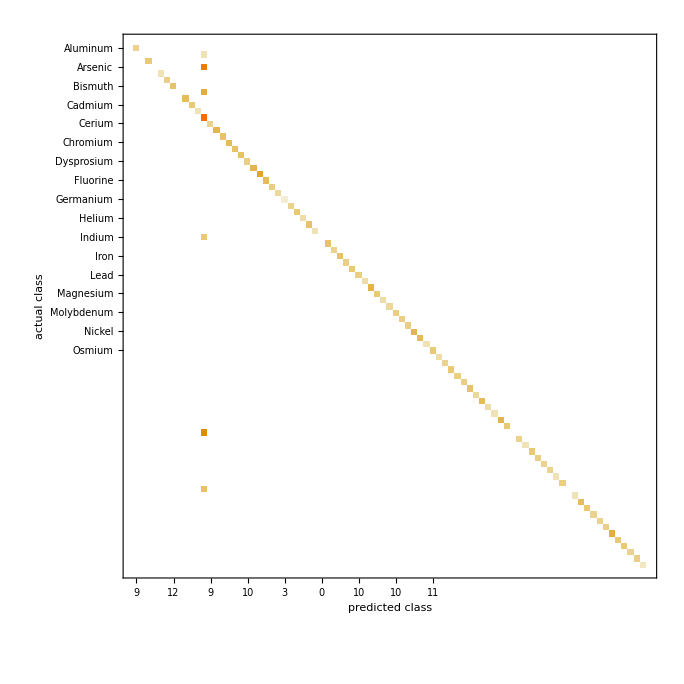

Confusion matrix for classifier trained on wavelength data [including compounds]:

Learning curve for classifier trained on images

```mathematica
-Graphics--Graphics-
```

Confusion matrix for classifier trained on images:

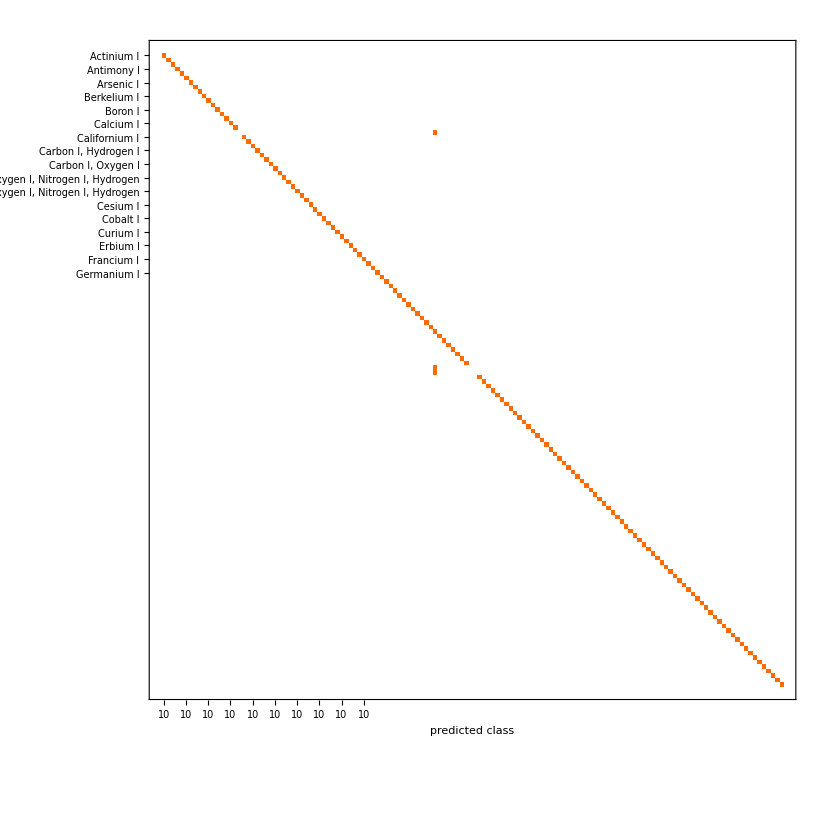

#### Data Sources Links/References

Ralchenko, Y., et al. “NIST Atomic Spectra Database (Version 4.0.1).” National Institute of Standards and Technology
https://www.nist.gov/pml/atomic-spectra-database

#### Future Directions

In the future, the classifier function can be expanded to support more ions and combinations, and accuracy can be improved by training Classify on more data samples. The Code section of this notebook shows step-by-step the process followed to create the spectrum classifier function, and can be reproduced to generate more data, add it to the existent data and retrain the classifier. The classifier is trained on highly accurate and detailed data, so it does not work very well with lower definition spectra. This can be improved by adding lower definition data to the classifier. It can also be expanded to account for Doppler shifting, which is very useful for investigating the motion of light sources and has several astrophysical and cosmological applications. Image manipulation can also be implemented to expand the classifier’s ability to determine the chemical composition from absorption spectra and perhaps have an option to identify if the input is an emission spectrum or an absorption spectrum.

#### Background Info Links/References

Condon, E. U., & Shortley, G. (1999). The theory of atomic spectra. New York: Cambridge University Press.
Sobelʹman, I. I. (1996). Atomic spectra and radiative transitions. Berlin: Springer.

How elements are formed. (n.d.). Retrieved from https://www.sciencelearn.org.nz/resources/1727-how-elements-are-formed

#### Keywords

Provide keywords as items

< spectrum>

<spectroscopy>

<classify>

#### Other information

The set up of this project and the data generation give emission spectra by default since it is built on the SpectralLineData function and its background data. Absorption spectra can be generated from emission spectra by image manipulation.